# GSI ALC Database Demo

Welcome to the GSI ALC Database Demo-script! This notebook is designed to demonstrate how you can interact with and explore the Absolute Lymphocyte Count (ALC) database developed at GSI.

Please note that this is not a rigorous scientific analysis. Instead, it serves as a practical demo with sample code to show how you can “play” with this database and extract useful insights.

## Step 1: Load the Dataset

We will now read the main dataset (datasets_table.xlsx) into a DataFrame using pandas. This dataset contains information about multiple publications and related data points.

```mathematica
(*Import the Excel file into Mathematica*)
database=Import[NotebookDirectory[]<>"datasets_table.xlsx","Data"][[1]];
(*Convert to a Dataset for easier manipulation*)
data=Dataset[AssociationThread[database[[1]],#]&/@Rest[database]];

(*Define transformation functions for specific columns*)
transforms=<|
"Dataset ID"->Round,
"Radiation type"->(If[StringQ[#],StringTrim/@StringSplit[#,","],{}]&),
"Therapy modality"->(If[StringQ[#],StringTrim/@StringSplit[StringReplace[#,"*"->""],","],{}]&),
"# Patients"->(If[StringQ[#]&&StringTrim[#]==="",Null,Round[If[StringQ[#],ToExpression[#],#]]]&),
"# Datapoints"->Round,
"Has recovery data"->(#==="True"&),
"Normalized"->(#==="True"&),
"Combined dataset"->(#==="True"&),
"Estimated EoT Time (wk)"->(ToExpression[StringReplace[ToString[#],"*"->""]]&),
"Estimated RLC at EoT (%)"->(ToExpression[StringReplace[ToString[#],"*"->""]]&),
"Year"->Round,
"Derived datasets"->(If[StringQ[#],Module[{s=#},(*Replace parentheses and fix stray commas before closing braces*)s=StringReplace[s,{"("->"{",")"->"}",",)"->"}"}];
(*Replace an empty string with "Null"*)s=If[StringTrim[s]==="","Null",s];
(*Convert the string to an expression and convert reals to integers*)ToExpression[s]/. r_Real:>Round[r]],#]&)
|>;

(*Apply the transformations to every row in the Dataset*)
data=data[All,Function[row,AssociationMap[If[KeyExistsQ[transforms,#],transforms[#][row[#]],row[#]]&,Keys[row]]]];
data=data[All,Function[row,ReplacePart[row,"Derived datasets"->row["Derived datasets"]/. r_Real:>Round[r]]]];

data
```

```mathematica
data[[93]][["Derived datasets"]][[0]]
```

#### Let’s make some statistics on the entries in the data

```mathematica
(*Count key statistics*)(*Total number of rows (datasets)*)
nDatasets=data[Length];
nPapers=data[All,"Publication tag"]//Normal//DeleteDuplicates//Length;
nDois=data[All,"DOI"]//Normal//DeleteDuplicates//Length;
nHasRecovery=Total[Boole/@(data[All,"Has recovery data"]//Normal)];
nNormalized=Total[Boole/@(data[All,"Normalized"]//Normal)];
nPooledDatasets=Total[Boole/@(data[All,"Combined dataset"]//Normal)];
nPapersWithPooledData=data[Select[#["Combined dataset"]===True&],"Publication tag"]//Normal//DeleteDuplicates//Length;
(*Derived datasets counts*)
nParentDatasets=Total[Boole/@(ListQ/@(data[All,"Derived datasets"]//Normal))];
nDaughterDatasets=Total[Boole/@(IntegerQ/@(data[All,"Derived datasets"]//Normal))];
nPapersWithParents=data[Select[ListQ[#["Derived datasets"]]&],"Publication tag"]//Normal//DeleteDuplicates//Length;
nPapersWithDaughters=data[Select[IntegerQ[#["Derived datasets"]]&],"Publication tag"]//Normal//DeleteDuplicates//Length;
(*Individual and undefined datasets*)
nIndividDatasets=Count[data[All,"# Patients"]//Normal,1];
nIndividPapers=data[Select[#["# Patients"]===1&],"Publication tag"]//Normal//DeleteDuplicates//Length;
nUndefinedDatasets=Total[Boole/@(ListQ/@(data[All,"Estimated EoT Time (wk)"]//Normal))];
nUndefinedPapers=data[Select[ListQ[#["Estimated EoT Time (wk)"]]&],"Publication tag"]//Normal//DeleteDuplicates//Length;
undefCounts=<|"Estimated EoT Time"->Count[data[All,"Estimated EoT Time (wk)"]//Normal,_Missing],"# Patients"->Count[data[All,"# Patients"]//Normal,Null]|>;
(*Recovery and normalized data stats:count unique papers for True values*)
nPapersWithRecovery=data[Select[#["Has recovery data"]===True&],"Publication tag"]//Normal//DeleteDuplicates//Length;
nPapersWithNormalized=data[Select[#["Normalized"]===True&],"Publication tag"]//Normal//DeleteDuplicates//Length;

(*Format and print the results*)
results=StringTemplate["Number of datasets (papers): `ndatasets` (`npapers`)\nNumber of unique DOIs: `ndois` — DOIs match papers: `doiMatch`\nDatasets (papers) with recovery data: `nhasrecovery` (`npaperswithrecovery`)\nDatasets (papers) with normalized data: `nnormalized` (`npaperswithnormalized`)\nPooled datasets (papers): `npool` (`npaperswithpool`)\nParent datasets (papers): `nparent` (`npaperswithparents`)\nDaughter datasets (papers): `ndaughter` (`npaperswithdaughters`)\nDatasets (papers) on individuals: `nindivid` (`npapersindivid`)\nDatasets (papers) with undefined therapy duration: `nundefined` (`npapersundefined`)\nUndefined 'Estimated EoT Time': `undefEoT`\nUndefined '# Patients': `undefPatients`"];

Print[results[<|"ndatasets"->nDatasets,"npapers"->nPapers,"ndois"->nDois,"doiMatch"->ToString[nPapers==nDois],"nhasrecovery"->nHasRecovery,"npaperswithrecovery"->nPapersWithRecovery,"nnormalized"->nNormalized,"npaperswithnormalized"->nPapersWithNormalized,"npool"->nPooledDatasets,"npaperswithpool"->nPapersWithPooledData,"nparent"->nParentDatasets,"npaperswithparents"->nPapersWithParents,"ndaughter"->nDaughterDatasets,"npaperswithdaughters"->nPapersWithDaughters,"nindivid"->nIndividDatasets,"npapersindivid"->nIndividPapers,"nundefined"->nUndefinedDatasets,"npapersundefined"->nUndefinedPapers,"undefEoT"->undefCounts["Estimated EoT Time"],"undefPatients"->undefCounts["# Patients"]|>]]
```

Number of datasets (papers): 142 (52)
Number of unique DOIs: 52 — DOIs match papers: True
Datasets (papers) with recovery data: 66 (34)
Datasets (papers) with normalized data: 30 (7)
Pooled datasets (papers): 10 (9)
Parent datasets (papers): 10 (9)
Daughter datasets (papers): 27 (9)
Datasets (papers) on individuals: 57 (7)
Datasets (papers) with undefined therapy duration: 0 (0)
Undefined 'Estimated EoT Time': 0
Undefined '# Patients': 8

#### Let’s look at datasets with undefined EoT-time and number of patients

```mathematica
undefinedDatasetsList=data[Select[#["Estimated EoT Time (wk)"]===Null&]];
undefinedPatientsList=data[Select[#["# Patients"]===Null&]];
Print["Datasets with Undefined Estimated Therapy Duration:"];
Print[undefinedDatasetsList[All,"Publication tag"]];
Print["\n-=-=-=-=-=-=-=-=-=-=-=-=-=-\n"];
(*Display the list of datasets with undefined'# of patients'*)
Print["Datasets with Undefined Number of Patients:"];
Print[undefinedPatientsList[All,"Publication tag"]];
```

Datasets with Undefined Estimated Therapy Duration:

-=-=-=-=-=-=-=-=-=-=-=-=-=-

Datasets with Undefined Number of Patients:

## Step 2: Display and Plot Basic Statistics

In this section, we calculate and display basic statistics for several key columns in the dataset:
- Number of Patients
- Number of Datapoints
- Estimated Therapy Duration (in weeks)
- Estimated Relative Lymphocyte Count (RLC) at End of Therapy (EoT)

For each variable, we will:
1. Calculate the mean, median, and range.
2. Plot a histogram to visualize the distribution of values.

-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-

Number of Patients Statistics:

Mean: 98.72

Median: 21

Range: 1 - 920

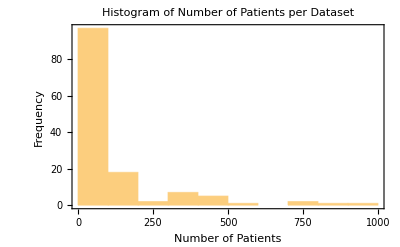

-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-

Number of Patients (excluding individual datasets) Statistics:

Mean: 171.05

Median: 95

Range: 4 - 920

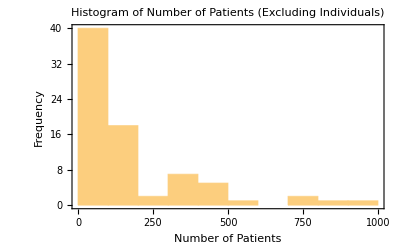

-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-

Number of Datapoints Statistics:

Mean: 11.69

Median: 7

Range: 3 - 81

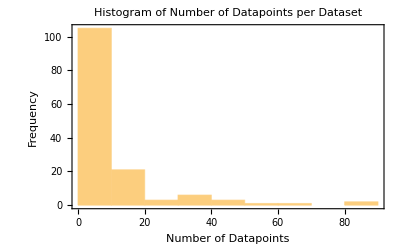

-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-

Estimated Therapy Duration (weeks) Statistics:

Mean: 5.61

Median: 5.60

Range: 0.57 - 15

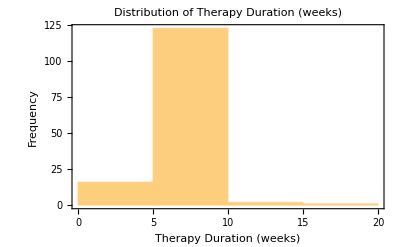

-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-

Estimated RLC at EoT (%) Statistics:

Mean: 27.52

Median: 22.80

Range: 0.9 - 78.3

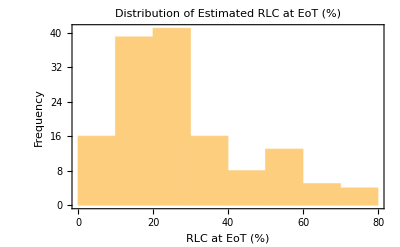

```mathematica
(*Helper function to display basic statistics*)displayStatistics[title_,mean_,median_,{min_,max_}]:=Module[{},Print["\n-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-\n"];
Print[title<>" Statistics:"];
Print["Mean: "<>ToString[NumberForm[mean,{Infinity,2}]]];
Print["Median: "<>ToString[NumberForm[median,{Infinity,2}]]];
Print["Range: "<>ToString[min]<>" - "<>ToString[max]];];

(*Helper function to plot histograms*)
plotHistogram[dataList_,title_,xlabel_,bins_:30]:=Histogram[dataList,{bins},Frame->True,FrameLabel->{xlabel,"Frequency"},PlotLabel->title,ImageSize->{400,300}];

(*Assuming'data' is your Dataset.Extract columns as normal lists:*)
patientsList=data[All,"# Patients"]//Normal;
datapointsList=data[All,"# Datapoints"]//Normal;
durationList=data[All,"Estimated EoT Time (wk)"]//Normal;
rlcList=data[All,"Estimated RLC at EoT (%)"]//Normal;

(*-------------------------*)
(*Section 1:Number of Patients*)
(*-------------------------*)

meanPatients=N[Mean[DeleteCases[patientsList,Null]]];
medianPatients=Median[DeleteCases[patientsList,Null]];
rangePatients={Min[DeleteCases[patientsList,Null]],Max[DeleteCases[patientsList,Null]]};

displayStatistics["Number of Patients",meanPatients,medianPatients,rangePatients];
Print[plotHistogram[patientsList,"Histogram of Number of Patients per Dataset","Number of Patients",100]];

(*Excluding individual datasets (i.e.where "# Patients">1)*)
patientsListNoIndivid=Select[DeleteCases[patientsList,Null],#>1&];
meanPatientsNoIndivid=N[Mean[patientsListNoIndivid]];
medianPatientsNoIndivid=Median[patientsListNoIndivid];
rangePatientsNoIndivid={Min[patientsListNoIndivid],Max[patientsListNoIndivid]};

displayStatistics["Number of Patients (excluding individual datasets)",meanPatientsNoIndivid,medianPatientsNoIndivid,rangePatientsNoIndivid];
Print[plotHistogram[patientsListNoIndivid,"Histogram of Number of Patients (Excluding Individuals)","Number of Patients",100]];

(*-------------------------*)
(*Section 2:Number of Datapoints*)
(*-------------------------*)

meanDatapoints=N[Mean[datapointsList]];
medianDatapoints=Median[datapointsList];
rangeDatapoints={Min[datapointsList],Max[datapointsList]};

displayStatistics["Number of Datapoints",meanDatapoints,medianDatapoints,rangeDatapoints];
Print[plotHistogram[datapointsList,"Histogram of Number of Datapoints per Dataset","Number of Datapoints",10]];

(*-------------------------*)
(*Section 3:Estimated Therapy Duration (wk)*)
(*-------------------------*)
(*Exclude undefined values (here we assume undefined are represented by Null)*)
validDurationList=DeleteCases[durationList,Null];

meanDuration=N[Mean[durationList]];
medianDuration=Median[durationList];
rangeDuration={Min[durationList],Max[durationList]};

displayStatistics["Estimated Therapy Duration (weeks)",meanDuration,medianDuration,rangeDuration];
Print[plotHistogram[validDurationList,"Distribution of Therapy Duration (weeks)","Therapy Duration (weeks)",5]];

(*-------------------------*)
(*Section 4:Estimated RLC at EoT (%)*)
(*-------------------------*)
validRlcList=DeleteCases[rlcList,Null];

meanNadir=Mean[rlcList];
medianNadir=Median[rlcList];
rangeNadir={Min[rlcList],Max[rlcList]};

displayStatistics["Estimated RLC at EoT (%)",meanNadir,medianNadir,rangeNadir];
Print[plotHistogram[validRlcList,"Distribution of Estimated RLC at EoT (%)","RLC at EoT (%)",10]];
```

## Step 3: Load Data from File Paths

In this step, we will read data from the files specified in the `Relative path` column and populate the corresponding cells in the DataFrame.
Each file contains measurements of x, y, x_low_err, x_high_err, y_low_err, and y_high_err. These values will be converted into lists and assigned to the relevant columns.

```mathematica
readData[filePath_String]:=Module[{txt,lines,data,cols},Check[(*Import the entire file as text*)txt=Import[filePath,"Text"];
(*Split into lines*)lines=StringSplit[txt,"\n"];
(*Drop the first 8 header lines and trim each remaining line*)data=Map[StringTrim,Drop[lines,8]];
(*For each line,split by ";" and convert each piece to a number*)data=Map[ToExpression/@StringSplit[#,";"]&,data];
(*Define the column names*)cols={"x","y","x_low_err","x_high_err","y_low_err","y_high_err"};
(*Create an association mapping each column to its list of values*)AssociationThread[cols,Transpose[data]],(*If something goes wrong,return empty lists for all columns*)AssociationThread[{"x","y","x_low_err","x_high_err","y_low_err","y_high_err"},ConstantArray[{},6]]]];


(* ::Section::*)
(*Assume data is already imported as a Dataset.Convert it to a normal list of associations for manipulation.*)

dataList=Normal[data];

(*Add new keys for the data columns and initialize them to Null*)
dataList=Map[Join[#,<|"x"->Null,"y"->Null,"x_low_err"->Null,"x_high_err"->Null,"y_low_err"->Null,"y_high_err"->Null|>]&,dataList];

(*Get current working directory.(NotebookDirectory[] returns the directory of the current notebook.)*)
currentFolder=NotebookDirectory[];

(* ::Section::*)
(*Iterate over each row and populate the new columns with lists from the corresponding data files*)

dataList=Map[Function[row,Module[{filePath,fileData},filePath=row["Relative path"];
fileData=readData[FileNameJoin[{currentFolder,filePath}]];
row~Join~<|"x"->fileData["x"],"y"->fileData["y"],"x_low_err"->fileData["x_low_err"],"x_high_err"->fileData["x_high_err"],"y_low_err"->fileData["y_low_err"],"y_high_err"->fileData["y_high_err"]|>]],dataList];


(*Optionally convert the updated list of associations back into a Dataset*)
data=Dataset[dataList];

(*Display the updated Dataset*)
data
data[[1]][["x_low_err"]]
```

#### Processing Error Values

The x_err and y_err lists represent the positions of the lower and upper error limits. To convert them into actual uncertainty values (error magnitudes), we need to process them as follows:
- x_err → |x - x_err|
- y_err → |y - y_err|

```mathematica
data=data[All,Function[row,row~Join~<|"x_low_err"->(row["x"]-row["x_low_err"]),"x_high_err"->(row["x_high_err"]-row["x"]),"y_low_err"->(row["y"]-row["y_low_err"]),"y_high_err"->(row["y_high_err"]-row["y"])|>]];
data[[1]][["x_low_err"]]
```

#### Let’s look at some dataset with particular data ID

```mathematica
id = 1;
data[[id]]
```

## Step 4: Plot Datasets

In this step, we will plot all datasets into a single pad. Error bars and datasets from Chanana et al., 1976 and Weeke et al., 1970, were omitted for better picture.

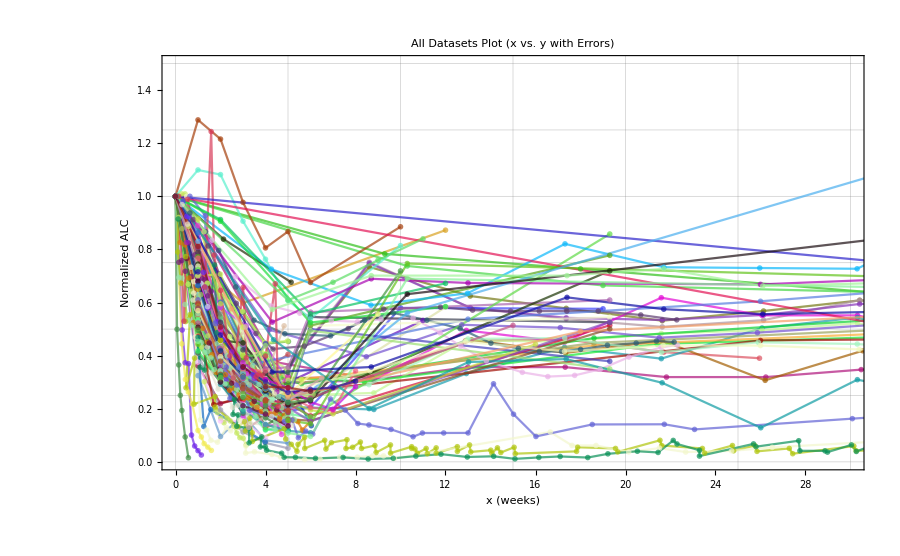

```mathematica
(*Assume dataList is your list of associations;for example:*)(*dataList=Normal[data];*)plots=DeleteCases[Table[If[MemberQ[{"Chanana76","Weeke70"},row["Publication tag"]]||row["y"][[1]]==0,Nothing,(*Skip this dataset by returning Nothing*)Module[{x,y,xlow,xhigh,ylow,yhigh,pts,errGraphics,dataID},
dataID=row["Dataset ID"];
pubTag = row["Publication tag"];
dataPath = row["Relative path"];
x=row["x"];
y=row["y"];
xlow=row["x_low_err"];
xhigh=row["x_high_err"];
ylow=row["y_low_err"];
yhigh=row["y_high_err"];
(*Normalize y and its error arrays by the first y value*)y=y/y[[1]];
ylow=ylow/y[[1]];
yhigh=yhigh/y[[1]];
pts=Transpose[{x,y}];
(*Construct error bars as Graphics primitives:For each point,a vertical line and a horizontal line are drawn.*)errGraphics=Graphics[Table[{Gray,Line[{{x[[i]],y[[i]]-ylow[[i]]},{x[[i]],y[[i]]+yhigh[[i]]}}],Line[{{x[[i]]-xlow[[i]],y[[i]]},{x[[i]]+xhigh[[i]],y[[i]]}}]},{i,Length[x]}]];
ListPlot[pts,Joined->True,PlotMarkers->{"o",Medium},PlotStyle->{RandomColor[],Opacity[0.7]},PlotRange->{{0,30},{0,1.5}},AxesLabel->{"x (weeks)","Normalized ALC"},GridLines->{Range[0,30,5],Range[0,1.5,0.25]},ImageSize->600,PlotLabel->"Dataset ID: "<>ToString[dataID]<>"\nPublication tag: "<>pubTag<>"\nPath: "<>dataPath]]],{row,dataList}],Nothing];

(*Combine all valid plots into one figure using Show.Sequence@@is used to splice the list of graphics into the arguments for Show.*)
Show[Sequence@@plots,Frame->True,FrameLabel->{"x (weeks)","Normalized ALC"},PlotRange->{{0,30},{0,1.5}},GridLines->{Range[0,30,5],Range[0,1.5,0.25]},ImageSize->{900,600},PlotLabel->"All Datasets Plot (x vs. y with Errors)"]
```

Plotting all datasets together results in a rather noisy picture due to the diversity in the data—different datasets represent varying numbers of patients, cancer types, and therapy modalities. Despite this complexity, certain trends and patterns remain visible.

#### Let’s plot only one plot (choosing dataset_id)

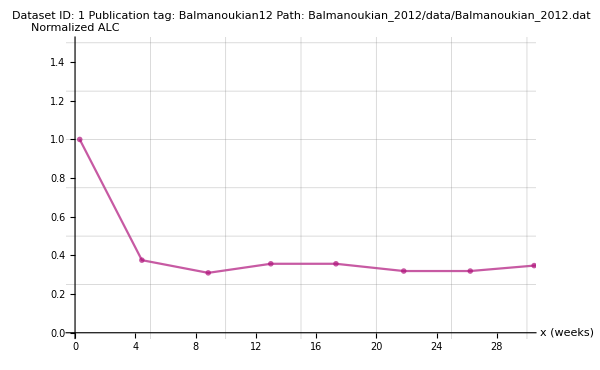

```mathematica
id = 1;
plots[[id]]
```

## This concludes the demo.

Feel free to explore the code further and perform your own analyses. Don’t hesitate to experiment, modify, and extract additional insights from the dataset. 
Good luck and happy coding!